```mathematica
SystemOpen@"https://www.navcen.uscg.gov/pdf/lightLists/LightList%20V1.pdf"
```

```mathematica
URL@"https://www.navcen.uscg.gov/?pageName=lightListWeeklyUpdates"
```

URL[https://www.navcen.uscg.gov/?pageName=lightListWeeklyUpdates]

```mathematica
ExportString[XMLElement["tag",{"foo" ->"1","bar" -> "three"},{"contents"}],"XML"]
```

<tag foo='1' bar='three'>contents</tag>

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/aarone/Desktop/Data-Curation-Training/Part3/USCG_light_list

```mathematica
FileNames[]
```

{.DS_Store,index.html?Do=weeklyLLCXML&id=1,scrape.nb}

```mathematica
lightsxml=Import["index.html?Do=weeklyLLCXML&id=1",{"XML","XML"}];
```

```mathematica
lightsxml//.XMLElement[tag_,att_,cont_]:>OpenerView[{tag,{att,Column@cont}}]
```

$Aborted[]

```mathematica
lightsxml
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Encoding→UTF-8]},XMLElement[root,{1,1},{XMLElement[{http://www.w3.org/2001/XMLSchema,schema},{},{XMLElement[{http://www.w3.org/2001/XMLSchema,element},{name→dataroot},{XMLElement[{http://www.w3.org/2001/XMLSchema,complexType},{},{XMLElement[{http://www.w3.org/2001/XMLSchema,sequence},{},{XMLElement[{http://www.w3.org/2001/XMLSchema,element},{ref→V…ru,1,1},{}]}],1}]}],1}],1}],{}]
 |  |  |  |

```mathematica
schema=Cases[lightsxml,XMLElement[{"http://www.w3.org/2001/XMLSchema","schema"},_,schema_]:>schema,Infinity];
```

```mathematica
schema//.XMLElement[tag_,att_,cont_]:>OpenerView[{tag,{att,Column@cont}}]
```

{{,}}

```mathematica
lights0=Cases[lightsxml,XMLElement["Vol_x0020_1_x0020_D1_x0020_LL_x0020_corr_x0020_thru",_,l_]:>l,Infinity]
```

{1,8782,{XMLElement[District,{},{1}],XMLElement[LLNR,{},{40110}],XMLElement[XREF,{},{}],XMLElement[Aid_x0020_Name,{},{Indian Point Lighted Buoy 3}],XMLElement[Aid_x0020_Type,{},{PA}],XMLElement[Position_x0020__x0028_Latitude_x0029_,{},{44-57-18.700N}],XMLElement[1],1,XMLElement[1],XMLElement[Height,{},{}],XMLElement[Location,{},{}],XMLElement[Structure,{},{Green.}],XMLElement[Remarks,{},{Private Aid}],XMLElement[RACN_x0020_Morse_x0020_Char,{},{}]}}
 |  |  |  |

```mathematica
First/@#&/@lights0//Tally
```

{{{District,LLNR,XREF,Aid_x0020_Name,Aid_x0020_Type,Position_x0020__x0028_Latitude_x0029_,Position_x0020__x0028_Longitude_x0029_,Characteristic,Both_x002F_Night_x002F_Day,Height,Range,Location,Structure,Remarks,RACN_x0020_Morse_x0020_Char},1830},{{District,LLNR,XREF,Aid_x0020_Name,Aid_x0020_Type,Position_x0020__x0028_Latitude_x0029_,Position_x0020__x0028_Longitude_x0029_,Characteristic,Both_x002F_Night_x002F_Day,Height,Location,Structure,Remarks,RACN_x0020_Morse_x0020_Char},993},{{District,LLNR,XREF,Aid_x0020_Name,Aid_x0020_Type,Position_x0020__x0028_Latitude_x0029_,Position_x0020__x0028_Longitude_x0029_,Height,Location,Structure,Remarks,RACN_x0020_Morse_x0020_Char},5961}}

```mathematica
First/@#&/@lights0//Flatten//DeleteDuplicates
```

```mathematica
propertyrules = 
{"District"->"District","LLNR"-> "LightListNumber","XREF"-> "XREF","Aid_x0020_Name"->"Name","Aid_x0020_Type"->"Type","Position_x0020__x0028_Latitude_x0029_"->"Latitude","Position_x0020__x0028_Longitude_x0029_"->"Longitude","Characteristic"->"Characteristic","Both_x002F_Night_x002F_Day"->"NightDayOrBoth","Height" -> "Height","Range"-> "Range","Location"->"Location","Structure"->"Structure","Remarks"->"Remarks","RACN_x0020_Morse_x0020_Char"->"Morse"}
```

{District→District,LLNR→LightListNumber,XREF→XREF,Aid_x0020_Name→Name,Aid_x0020_Type→Type,Position_x0020__x0028_Latitude_x0029_→Latitude,Position_x0020__x0028_Longitude_x0029_→Longitude,Characteristic→Characteristic,Both_x002F_Night_x002F_Day→NightDayOrBoth,Height→Height,Range→Range,Location→Location,Structure→Structure,Remarks→Remarks,RACN_x0020_Morse_x0020_Char→Morse}

```mathematica
Tally[Head/@propertyrules]
```

{{Rule,15}}

```mathematica
Tally[Length/@(Last/@Flatten[lights0])]
```

{{1,74942},{0,37942}}

```mathematica
XMLElement[t_,{},c_]:>Rule[t,c]
```

```mathematica
lights1=lights0/.XMLElement[t_,{},c_]:>Rule[(t/.propertyrules),Replace[c,{{thing_}:>thing,{}->Missing["NotAvailable"]}]];
```

```mathematica
RandomSample[lights1,3]
```

```mathematica
{{"District"->"1","LightListNumber"->"18285","XREF"->Missing["NotAvailable"],"Name"->"Providence River Approach Channel Lighted Buoy 11","Type"->"FD","Latitude"->"41-41-54.095N","Longitude"->"071-19-28.957W","Characteristic"->"Fl G 2.5s","NightDayOrBoth"->"Night","Height"->Missing["NotAvailable"],"Range"->"3","Location"->Missing["NotAvailable"],"Structure"->"Green.","Remarks"->"Replaced by can when endangered by ice.","Morse"->Missing["NotAvailable"]},{"District"->"1","LightListNumber"->"24515","XREF"->Missing["NotAvailable"],"Name"->"Housatonic River Channel Buoy 44","Type"->"FD","Latitude"->"41-14-35.358N","Longitude"->"073-05-46.930W","Height"->Missing["NotAvailable"],"Location"->Missing["NotAvailable"],"Structure"->"Red nun.","Remarks"->Missing["NotAvailable"],"Morse"->Missing["NotAvailable"]},{"District"->"1","LightListNumber"->"11285","XREF"->Missing["NotAvailable"],"Name"->"Dorchester Bay Basin Channel Buoy 6","Type"->"PA","Latitude"->"42-18-18.700N","Longitude"->"071-03-05.600W","Height"->Missing["NotAvailable"],"Location"->Missing["NotAvailable"],"Structure"->"Red nun.","Remarks"->"Private Aid","Morse"->Missing["NotAvailable"]}}
```

```mathematica
lightassoc=Association/@lights1;
```

```mathematica
RandomSample[lightassoc,2]
```

{<|District→1,LightListNumber→7705,XREF→Missing[NotAvailable],Name→Coast Guard Pierhead Light,Type→FD,Latitude→43-38-59.896N,Longitude→070-15-12.872W,Characteristic→Fl Y 4s,NightDayOrBoth→Night,Height→18,Range→4,Location→Missing[NotAvailable],Structure→On dolphin.,Remarks→Missing[NotAvailable],Morse→Missing[NotAvailable]|>,<|District→1,LightListNumber→14744.5,XREF→Missing[NotAvailable],Name→Marstons Mills River Buoy 16,Type→PA,Latitude→41-38-41.678N,Longitude→070-24-31.806W,Height→Missing[NotAvailable],Location→Missing[NotAvailable],Structure→Red nun.,Remarks→Private Aid,Morse→Missing[NotAvailable]|>}

```mathematica
Tally[StringTake[lightassoc[[All,"Latitude"]],-1]]
```

{{N,8784}}

```mathematica
Tally[StringTake[lightassoc[[All,"Longitude"]],-1]]
```

{{W,8784}}

```mathematica
FromDMS["20°3'1.45\"N"]
```

```mathematica
lightassoc[[All,"Structure"]]//Tally
```

{{Yellow.,139},{Granite conical tower. 65,1},{Cylindrical gray granite tower. 41,1},{White tower. 47,1},{53,1},{White tower attached to dwelling. 77,1},{Red and white stripes with red spherical topmark.,62},{White conical tower. 67,1},{Green can.,2315},{Red nun.,2435},{Green.,687},{Red.,812},{White conical tower connected to dwelling. 71,1},{Missing[NotAvailable],167},{Red nun with green bands.,21},{White conical tower connected to dwelling. 88,1},{Gray conical tower, connected to dwelling. 133,1},{Gray conical tower. 59,1},{White conical tower. 58,1},{Black and red bands with two black spherical topmarks; can.,18},{White with orange bands, can.,12},{White conical tower. 45,2},{White cylindrical tower.,2},{Gray granite conical tower.,1},{Iron spindle.,1},{White conical tower. 111,1},{White and orange.,64},{On light gray conical granite tower. 98,1},{On white conical tower. 89,1},{On gray conical tower. 87,1},{TR on white skeleton tower.,6},{On white tower. 45,1},{White conical tower. 66,1},{Conical tower, upper part red, lower part white.,1},{White conical tower. 43,1},{On white tower. 70,1},{White tower with red band in the middle. 70,1},{Steel tripod with mast.,1},{Red brick tower. 51,1},{Tower on red square on 3 red piles with large red tube in center, worded BUZZARDS on sides. 68,1},{Red-brick octagonal, pyramidal tower attached to dwelling. 67,1},{Yellow,9},{White conical tower with red stripe. 168,1},{Skeleton tower. 75,1},{Red and white stripes.,10},{Yellow nun.,16},{Yellow boat-shaped buoy.,1},{White conical tower on black cylindrical pier.,1},{SG on iron spindle.,14},{NG on skeleton tower.,18},{White skeleton tower surmounted by platform.,1},{On floating fish pens.,3},{White with orange bands.,64},{White tower with red stripes. 49,1},{TR on spindle.,48},{White tower. 42,2},{White and blue band, nun.,1},{NR on tower.,1},{NR on spindle.,11},{White and blue.,5},{SG on gray tower.,1},{TR on tower on end of breakwater.,1},{On white tower. 57,1},{TR on iron spindle.,10},{SG on spindle.,29},{White and with blue stripe, can.,1},{Green can with red bands.,23},{Red and white stripes; can.,3},{Gray granite tower. 109,1},{Red and green bands.,34},{White conical tower.,11},{Green and red bands.,33},{White tower. 40,2},{White ball with blue band marked CG.,1},{NW on spindle worded DANGER SUBMERGED BREAKWATER.,1},{White nun with blue stripe.,3},{Red,8},{NG on iron spindle.,2},{White stone tower.,2},{White pyramidal stone structure.,1},{White tower.,9},{White with blue band, nun.,2},{WHite and blue,1},{White tower. 36,1},{White tower connected to dwelling. 56,1},{JG on spindle.,1},{SG on skeleton tower.,83},{Yellow can.,37},{Green can,14},{White square tower.,3},{NR on skeleton tower.,24},{White and orange bands.,1},{White can with orange bands worded ROCK.,4},{White and black tower.,1},{Black and red bands with two black spherical topmarks.,11},{TR on skeleton tower.,81},{Gray conical tower.,1},{Tower, lower part conical, gray: upper part cylindrical, white brick; white bridge to shore.,1},{White tower. 51,1},{White with Orange bands.,3},{Tower.,2},{TR on iron spindle on stone monument.,1},{TR on spindle on stone monument.,1},{White house. 31,1},{TR on post on square stone base.,1},{White.,5},{On wood pile.,3},{White conical tower, black cylindrical foundation.,1},{White cylindrical tower. 24,1},{Gray stone square shaft pyramidal top.,1},{NW on spindle.,4},{White tower. 26,1},{SG on tripod.,1},{Red brick tower. 25,1},{Tower on white house.,1},{NG on spindle on square stone pyramid.,1},{TR on white skeleton tower, small white house.,1},{On pile.,76},{White and orange buoy marking aquaculture rafts.,4},{Gray Granite tower.,1},{Green and red bands; can.,31},{White cylindrical tower. 31,1},{SG on white skeleton tower.,2},{SG on pile.,200},{NB on pile.,2},{TR on pile.,172},{White conical tower. 79,1},{NR on pile.,4},{Green cylinder on monopile.,1},{White octagonal tower on dwelling. 59,1},{White with orange bands; spar.,1},{White house.,1},{SG on skeleton tower on caisson.,1},{SG on wooden spindle.,1},{On spindle.,1},{SG on skeleton tower, small white house.,1},{Conical tower.,1},{Green nun.,1},{TR on wooden spindle.,1},{Red nun,15},{NR on white skeleton tower.,3},{TR on white structure with small white house.,1},{Black and white square stone pyramid.,1},{NR on white square skeleton tower.,1},{White with orange bands worded DANGER.,2},{NR on spindle on red caisson.,1},{Shellfish raft.,2},{Red Nun.,4},{White tower. 80,1},{At base of Portland Head Light.,1},{Light-gray, conical, granite tower.,1},{TR on tower.,1},{On dolphin.,35},{SG on dolphin.,4},{NY on pile.,1},{Conical stone tower.,1},{White can with orange bands worded DANGER SUBMERGED BREAKWATER.,1},{NW on pile worded DANGER.,1},{White and orange nun.,3},{White ball with blue band.,1},{NG on pile.,2},{KRW on skeleton tower.,31},{White conical tower, fog signal house attached. 52,1},{TR on sectional spindle.,1},{NG on mast, on granite pier.,1},{Square concrete platform.,1},{On square concrete platform.,2},{White with orange bands worded NH DES.,11},{Green and red; can.,2},{NG on spindle.,3},{White and orange worded ROCKS.,1},{NW on skeleton tower worded DANGER ROUGH BAR.,1},{TR on red wooden slat pyramid on granite foundation.,1},{TR on skeleton tower on concrete foundation.,1},{White can with orange bands, worded ROCK.,1},{White tower with black trim.,1},{NR on iron spindle.,1},{Red and white stripes; spar.,10},{Red with white stripes; spar.,1},{White cylindrical tower; elevated walk to dwelling.,1},{SG on spindle on mound.,1},{NG on stone crib.,1},{SG on black cylindrical structure.,5},{TR on red cylindrical structure.,1},{TR on box on black cylindrical structure.,1},{TR on Spindle.,1},{White house and tower on brown square skeleton framework.,1},{NW on spindle on ledge.,1},{Red with green bands.,2},{NW on iron spindle.,1},{White pyramidal tower.,1},{White church spire.,1},{NR on conical granite monument.,1},{NR on staff on pyramidal granite base.,1},{Atop of white conical tower on concrete base.,1},{SG on gray skeleton tower on pile structure.,1},{SG on pile structure.,1},{GRG on pile.,1},{SG on staff on square, granite cribwork.,1},{SG on spindle on cribwork base.,1},{SG on pile on granite cribwork.,1},{Green with red bands.,1},{Square skeleton tower, brown to gallery, black above..,1},{SG on monopole.,2},{Black and red bands with two black spherical topmarks; can. .,1},{SG on multi-pile.,4},{White and blue nun.,2},{On pier.,3},{White and orange .,1},{White and Orange.,2},{White and orange buoy.,1},{White and orange buoys.,1},{SG on wood multi-pile.,3},{TR on wood multi-pile.,3},{SG on skeleton tower on piles.,1},{On top of cupola.,1},{Spindle on dock.,1},{White with blue stripes, nun.,1},{TR on dolphin.,1},{TR on pile structure.,1},{Black, white band midway of height; octagonal pyramid on square granite base.,1},{White can with orange bands.,3},{TR on grey skeleton tower on pile structure.,1},{NB on spindle.,2},{On pole.,9},{NW on pile worded DANGER ROCKS.,1},{NR on gray skeleton tower.,1},{NR on gray skeleton tower on pile structure.,1},{SG on black skeleton tower on pile structure.,1},{TR on skeleton tower on a pile structure.,1},{TR on skeleton tower on pile structure.,1},{TR on skeleton tower, on cylindrical base.,3},{White tower with dwelling.,1},{White, octagonal, pyramidal tower, white dwelling. 102,1},{Brown conical tower; upper half white.,1},{TR on skeleton tower on black cylindrical pier.,1},{NW on spindle on granite cribwork worded DANGER SUBMERGED JETTY.,1},{SG on skeleton tower on black cylindrical pier.,1},{TR on red cylindrical.,1},{Brick structure.,1},{Green,8},{TR,5},{SG,5},{TR on modular tower.,1},{Steel tower.,2},{White can with blue stripe.,1},{White square tower. 39,1},{White sign with black numerals.,1},{NW on Pole worded DANGER ROUGH BAR. 30,1},{Red and white sphere.,29},{Red and white.,6},{Red green bands: nun.,1},{Red can.,1},{Monopole steel tower mounted on a pile supported platform marked "MT".,1},{Red and green bands; nun.,24},{On pile at inshore end of weir.,1},{On piling.,4},{On pile at offshore end of trap.,3},{On pile at inshore end of trap.,2},{Modular tower.,1},{White and orange can.,11},{On tower.,2},{On skeleton tower.,12},{On white wooden building.,1},{On pile at offshore end of weir.,1},{White and red cylindrical tower. 30,1},{NB on black skeleton tower.,2},{White can with orange bands worded ROCKS.,1},{White can with orange bands worded ROCKS,2},{NW on Spindle. worded DANGER ROCKS.,1},{On monopole.,3},{Red and black bands; can.,1},{On wood dolphin.,1},{White sphere with blue stripe.,1},{White can with orange bands and diamond worded DANGER SUBMERGED JETTY.,1},{KRW on white wooden skeleton tower.,2},{White, cylindrical tower, footbridge to shore. 20,1},{Wharf end dolphin.,9},{Single metal post.,1},{White tower; small white building attached to west side of tower.,1},{White with orange bands and orange diamond.,1},{Marks ferry slip.,3},{NR on dolphin.,2},{Green can with red band.,1},{Red. nun.,1},{White with blue band.,1},{White cylindrical tower and dwelling on red caisson. 74,1},{KRW on white tower.,1},{KRW on white skeleton tower.,2},{SG on skeleton tower on cylindrical pier.,3},{TR on skeleton tower on cylindrical pier.,2},{SG on skeleton tower on cylindrical tower.,1},{White with orange bands worded DANGER ROCK.,1},{TR on gray skeleton tower on concrete base.,1},{TR on spindle on timber structure.,1},{Red and green; nun.,1},{Green Can.,4},{White conical tower on stone pier.,1},{White tower. 39,1},{White conical tower on granite base. b,1},{TR on skeleton tower on concrete base.,8},{Square granite tower, attached to white dwelling. 70,1},{Conical granite tower, upper half white. 34,1},{White stone tower. 33,1},{White dwelling.,1},{On bridge.,4},{On bridge abutment.,6},{TR on red skeleton tower.,2},{White octagonal tower.,1},{White conical tower on black cylindrical pier. 60,1},{TR on monopile.,2},{White conical tower on cylindrical pier.,1},{White octagonal tower.attached to dwelling.,1},{TR on skeleton tower on granite pier.,1},{White with orange bands worded ROCK.,4},{White conical tower, on brown cylindrical pier.,1},{Brick building.,1},{Brown over white conical tower.,1},{SG on black square skeleton tower.,1},{White conical tower. 51,1},{Octagonal tower, lower half white, upper half brown. 65,1},{White tower atop a house structure.,1},{SG on post on concrete base.,2},{TR on post on concrete base.,1},{Yellow spar.,4},{SG on white skeleton tower on base. 15,1},{TR on white cylindrical tower; red top.,1},{Square, gray granite tower attached to white building. 61,1},{Granite tower attached to dwelling, on granite pier. 45,1},{Green and red can.,2},{White conical tower, brown midway of height; brown cylinder.,1},{NW on pipe worded DANGER ROCKS.,1},{Square house with light tower.,1},{TR on skeleton tower, small house, concrete base.,1},{SG on skeleton tower, concrete base.,2},{TR on skeleton tower, concrete base.,1},{White with orange bands and diamond worded DANGER SUB PIPE.,1},{NW on pipe tower worded DANGER ROCKS.,1},{White with orange bands and diamond worded DANGER SUBMERGED PIPE.,1},{Pile.,4},{SB on pile.,2},{Black conical tower with white band in center. 64,1},{White conical tower on brown cylindrical pier. 49,1},{White square tower, dwelling attached. 103,1},{White octagonal tower. 94,1},{White octagonal house on brown cylindrical pier. 45,1},{White conical tower, dark red band midway of height. 35,1},{Gray, granite octagonal tower projection from house on pier. 35,1},{Black tower on granite house.,1},{White tower on granite dwelling on pier. 51,1},{Conical tower, upper half white, lower half brown, on black cylindrical pier. 52,1},{SG on tower.,2},{NR on skeleton tower. 62,1},{White stone tower, brown band midway of height; granite dwelling attached. 55,1},{TR on skeleton tower, concrete base on rocks.,1},{Red brick on granite pier; white band on southwest face of pier.,1},{Yellow, worded EBYRA.,1},{NB on skeleton tower. 60,1},{White can with orange bands and diamond worded ROCKS.,3},{On platform.,1},{White octagonal concrete tower.,1},{Red brick dwelling on square pier. 58,1},{White octagonal pyramidal tower. 89,1},{Pier dolphin.,3},{Dual light fixture on pier.,1},{Mooring island.,1},{On southeast bridge abutment of railroad bridge.,1},{TR on pile tower on concrete base.,1},{on pile.,1},{Grenn can.,1},{SG on skeleton tower on concrete base.,4},{SG on pipe tower pn consrete base.,1},{SG on pipe tower on concrete base.,6},{TR on pipe tower on concrete base.,10},{White and blue can.,1},{SY on pier.,1},{JG on pile.,2},{White globe on granite structure.,1},{White stone tower. 71,1},{Yellow square on pile.,1},{White with Orange bands, can.,1},{KRW and TR on skeleton tower.,4},{On dolphin center pile.,4},{TR on pipe tower.,1},{KRW and SG on skeleton tower.,1},{SG on pipe tower.,1},{Red with green band; nun.,1},{White with orange band; can.,2},{White can with orange band.,1},{TR on pile,3},{TR on pile. TR on pile.,1},{Tr on pile.,1},{SG on pile. SG on pile.,1},{KRW on pile.,5},{White and black.,1},{On dolphins.,1},{Daymark consists of white arrows, vertically arranged.,2},{White can with orange bands and diamond worded ROCK.,2},{Black conical tower.,1},{NW on piling worded DANGER ROCK.,1},{KWR on pile.,1},{White conical tower, middle part brown, on black cylindrical pier.,1},{White can with orange bands worded DANGER ROCKS.,1},{White conical tower, on red cylindrical pier.,1},{Green spar.,7},{Red spar.,7},{White nun.,1},{NW on spindle worded ROCKS.,2},{SG on tower on concrete base.,1},{White with orange bands; can.,4},{NW on spindle worded DANGER ROCK.,1},{On concrete pedestal.,2},{On Tower.,2},{On pile platform.,2},{White can with orange bands worded DANGER.,1},{Square concrete tower attached to dwelling on rectangular pier.,1},{TR on red cylindrical structure on pile.,1},{NR on skeleton tower, on caisson.,1},{White cylindrical structure.,1},{SG on black skeleton tower.,1},{SG on single pile.,1},{SG on skeleton tower on white base.,2},{TR on skeleton tower on white base.,1},{KGR on skeleton tower.,2},{White,1},{On wood platform.,1},{TR on tower on piles.,1},{White and orange,4},{On pile,13},{On post on dolphin.,1},{White tower and dwelling on piles.,1},{Single pile.,1},{White with blue stripes.,1},{Red skeleton tower.,1},{White can with orange bands and diamond worded DANGER ROCKS.,1},{TR on monopole.,1},{White with orange bands; can worded DANGER.,1},{Medal tower.,1},{White with orange bands worded DANGER ROCKS.,2},{On wood pole.,1},{Skeleton tower.,1},{On end of breakwater.,7},{SB on black skeleton tower.,1},{KWB on pile.,2},{TR on breakwall.,1},{SG on pole.,1},{SG on pile,4},{Green can..,1},{Green and red bands, can.,1},{Green arrow on pile.,1},{Red arrow on pile.,2},{TR on skeleton tower on piles.,1},{Tower on gate house.,1},{On metal tower.,1},{Red conical pipe structure.,1},{NR on four pile structure with pipe tower.,1},{Brown conical tower on black cylindrical pier.,1},{Octagonal brick tower, gray limestone base.,1},{White square skeleton tower. 75,1},{On Pole.,1},{On metal pole.,4},{Marks wharf dolphin.,1},{On wharf dolphin.,1},{Conical tower, lower half brown, upper half white, white base.,1},{Red skeleton tower, gallery at top.,1},{Brown octagonal shaped tower.,1},{On same structure as Staten Island Light.,1},{Conical tower, lower part white upper part brown; on black cylindrical pier. 54,1},{KGB (E section) KRW (Main section) on skeleton tower.,1},{KGB on skeleton tower.,1},{NB on skeleton tower. 30,1},{Spindle on rocks.,1},{NR on skeleton tower, red base.,1},{White with orange diamond marked SECURITY ZONE KEEP OUT.,9},{KRW on grey monopole.,1},{TR on square skeleton tower.,1},{TR on skeleton tower with base.,1},{TR on skeleton tower with red base.,1},{White conical tower on black conical pier.,1},{KRW on small white house on piles.,1},{KRW on black skeleton tower.,1},{KRW on orange pile.,1},{KRW on orange pole.,1},{On steel pole.,1},{On yellow pyramid tower.,1},{On steel pyramidal tower.,1},{KRW on tower.,1},{KRW on red tower.,1},{On wharf piling.,3},{Gray house on terminal chamber.,1},{On Pile.,1},{Green with red band.,1},{Atop fendering dolphin.,2},{JR on skeleton tower on white base.,1},{SG on skeleton tower on green base.,2},{On end of walkway over outfall pipe.,1},{WHite and Blue.,1},{Red lighthouse.,1},{TR on tower, small house at base.,1},{SG on same structure as Haverstraw Bay South Reach Range Front Light.,1},{On mooring dolphin.,2},{White nun with orange bands worded DANGER SUBMERGED OUTFALL.,2},{NG on skeleton tower, central column, small house, concrete base.,1},{NB on skeleton tower.,2},{SG on skeleton tower, small house.,1},{Gray rectangular structure.,2},{10X18 lighted platform.,1},{White with orange bands. Can.,5},{White conical tower on white dwelling.,1},{NW on dike worded DANGER SUBMERGED JETTY.,6},{SG on dike.,4},{TR on dike.,4},{Center bridge span.,1},{Green spar buoy.,3},{White can with orange bands and diamond.,3},{Grey conical tower.,1},{Red conical tower.,1},{SG on metal pile.,1},{TR on metal pile.,1},{On Grey conical tower.,1},{NW on skeleton tower worded DANGER JETTY.,2},{On pile cluster.,2},{NW on skeleton tower.,2},{In abandoned light house tower.,1},{NB on tower on concrete base.,1},{White square lighthouse on end of breakwater.,1},{White can with orange bands and diamond worded DANGER JETTY.,1},{NW on pile worded DANGER BREAKWATER.,1},{NW on pile worded DANGER SUBMERGED JETTY.,1},{Yellow sphere.,6},{White triangular lighthouse on end of breakwater.,1},{On white skeleton tower.,1},{Gray skeleton tower.,1},{On post.,1},{NG on gray skeleton tower.,2},{On grey skeleton tower.,1}}

```mathematica
llconv[l_String]:=FromDMS@StringReplace[StringReplace[StringReplace[l,"-"->"°",1],"-" -> "'",1],x_~~EndOfString:>("\""<>x)]
```

```mathematica
lightassoc2=Module[{rec = #},
rec["Latitude"]=llconv[rec["Latitude"]];
rec["Longitude"]=llconv[rec["Longitude"]];
rec["Coordinates"] = GeoPosition[{rec["Latitude"],rec["Longitude"]}];
rec["Height"] =Replace[rec["Height"],s_String:>Quantity[ToExpression[s],"Feet"]];
rec["Range"] =Replace[Replace[rec["Range"],s_String:>Quantity[ToExpression[s],"NauticalMiles"]],_Missing->Missing["NotAvailable"]];
rec["NightQ"] = Replace[rec["NightDayOrBoth"],{"Night"->True,"Both" -> True,"Day" -> False,_Missing-> Missing["NotAvailable"]}];
rec["DayQ"] = Replace[rec["NightDayOrBoth"],{"Day"->True,"Both" -> True,"Night" -> False,_Missing-> Missing["NotAvailable"]}];
KeyDropFrom[rec,{"Latitude","Longitude","NightDayOrBoth"}]
]&/@lightassoc;
```

```mathematica
lightds = Dataset[lightassoc2]
```

Dataset[<>]

```mathematica
GeoGraphics[Point/@lightds[Select[#DayQ&]][[All,"Coordinates"]]]
```

-Graphics-

```mathematica
lightds[Select[#DayQ&]][Select[!MatchQ[#Range,_Missing]&]]
```

Dataset[<>]

```mathematica
GeoDisk
```

```mathematica
GeoGraphics[Point/@lightds[Select[#DayQ&]][Select[!MatchQ[#Range,_Missing]&]][[All,"Coordinates"]]]
```

-Graphics-

```mathematica
GeoGraphics[GeoDisk[#Coordinates,#Range]&/@lightds[Select[#DayQ&]][Select[!MatchQ[#Range,_Missing]&]]]
```

-Graphics-

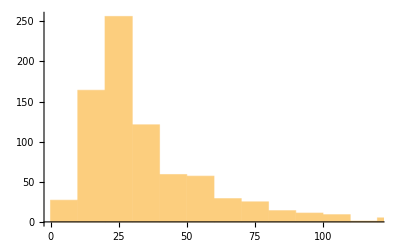

```mathematica
Histogram[lightds[[All,"Height"]]]
```